```mathematica
ClearAll["Global`*"]
```

```mathematica
t[n_,a_]:=Mod[n,a]-Mod[n-1,a]
s1[n_,0]:=1; s1[n_,k_] := s1[n,k]=s1[n,k]=Sum[ s1[Floor[n/j],k-1],{j,1,n}]
s1p[n_,k_]:=s1p[n,k]=Sum[(-1)^(k-j) Binomial[k,j]s1[n,j],{j,0,k}]

s2[n_,0]:=1;s2[n_,k_]:=s2[n,k]=s2[n,k]=Sum[t[j,3]s2[Floor[n/j],k-1],{j,1,n}]
s2p[n_,k_]:=s2p[n,k]=Sum[(-1)^(k-j) Binomial[k,j]s2[n,j],{j,0,k}]
s2pa[n_,a_]:=Sum[(-1)^j Binomial[a,j]3^j s1p[Floor[n/3^j],a],{j,0,a}]
s2a[n_,a_]:=Sum[(-1)^j Binomial[a,j]3^j s1[Floor[n/3^j],a],{j,0,a}]
s2m[n_,a_,b_]:=s2m[n,a,b]=Sum[(-1)^j Binomial[a,j]b^j s1[Floor[n/b^j],a],{j,0,a}]
s2mp[n_,a_,b_]:=s2mp[n,a,b]=Sum[(-1)^(a-j) Binomial[a,j]s2m[n,j,b],{j,0,a}]
s2p2[n_,k_]:=s2p2[n,k]=Sum[ t[j,3]s2p2[Floor[n/j],k-1],{j,2,n}];s2p2[n_,0]:=1

nmod[n_,b_]:=s2m[n,1,b]-s2m[n-1,1,b]
LAdd[n_,b_] := Sum[ b^k/k,{k,1,Log[b,n]}]
lin[n_,b_]:=Sum[(-1)^(k+1)/k s2mp[n,k,b],{k,1,Log[2,n]}]
lin2[n_]:=Sum[(-1)^(k+1)/k s2p[n,k],{k,1,Log[2,n]}]
lin3[n_]:=Sum[(-1)^(k+1)/k s1p[n,k],{k,1,Log[2,n]}]
```

```mathematica
s1p[100,3]
```

324

```mathematica
s2p2[100,5]
```

-9

```mathematica
s2p[100,5]
```

-9

```mathematica
s2mp[100,5,3]
```

-9

```mathematica
s2pa[100,5]
```

279

```mathematica
lin[100,2]+LAdd[100,2]
```

428/15

```mathematica
lin[100,3]+LAdd[100,3]
```

428/15

```mathematica
lin2[100]+LAdd[100,3]
```

428/15

```mathematica
lin3[100]
```

428/15

```mathematica
lin[100,5/2]+LAdd[100,5/2]
```

428/15

```mathematica
lin[100,2.1]
```

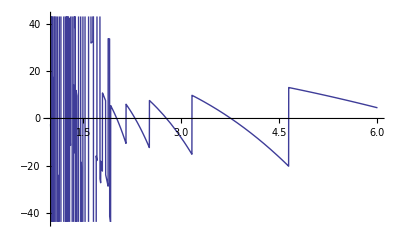

```mathematica
Plot[lin[100,n],{n,1,6}]
```

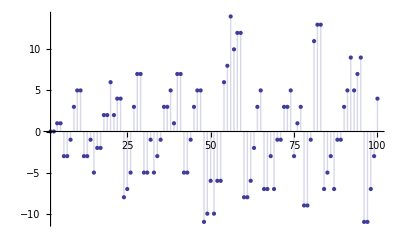

```mathematica
DiscretePlot[s2p[n,2],{n,2,100}]
```

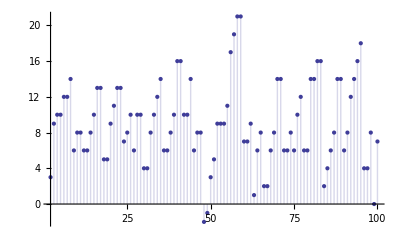

```mathematica
DiscretePlot[ s2pa[n,2],{n,2,100}]
```

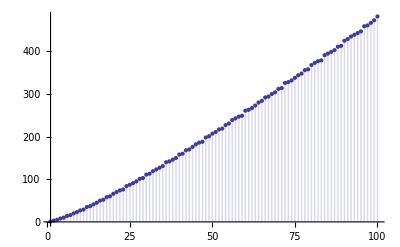

```mathematica
DiscretePlot[s1[n,2],{n,1,100}]
```

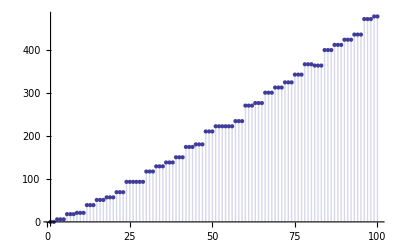

```mathematica
DiscretePlot[s1[n,2]-s2[n,2],{n,1,100}]
```

```mathematica
f[n_]:=(s1[2 n,2]-s2[2 n,2])/4
```

```mathematica
Table[{n,s2[n,1], Sum[(-1)^j Binomial[1,j]3^j s1[Floor[n/3^j],1],{j,0,2}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 0 | 0
4 | 1 | 1
5 | 2 | 2
6 | 0 | 0
7 | 1 | 1
8 | 2 | 2
9 | 0 | 0
10 | 1 | 1
11 | 2 | 2
12 | 0 | 0
13 | 1 | 1
14 | 2 | 2
15 | 0 | 0
16 | 1 | 1
17 | 2 | 2
18 | 0 | 0
19 | 1 | 1
20 | 2 | 2
21 | 0 | 0
22 | 1 | 1
23 | 2 | 2
24 | 0 | 0
25 | 1 | 1
26 | 2 | 2
27 | 0 | 0
28 | 1 | 1
29 | 2 | 2
30 | 0 | 0
31 | 1 | 1
32 | 2 | 2
33 | 0 | 0
34 | 1 | 1
35 | 2 | 2
36 | 0 | 0
37 | 1 | 1
38 | 2 | 2
39 | 0 | 0
40 | 1 | 1
41 | 2 | 2
42 | 0 | 0
43 | 1 | 1
44 | 2 | 2
45 | 0 | 0
46 | 1 | 1
47 | 2 | 2
48 | 0 | 0
49 | 1 | 1
50 | 2 | 2
51 | 0 | 0
52 | 1 | 1
53 | 2 | 2
54 | 0 | 0
55 | 1 | 1
56 | 2 | 2
57 | 0 | 0
58 | 1 | 1
59 | 2 | 2
60 | 0 | 0
61 | 1 | 1
62 | 2 | 2
63 | 0 | 0
64 | 1 | 1
65 | 2 | 2
66 | 0 | 0
67 | 1 | 1
68 | 2 | 2
69 | 0 | 0
70 | 1 | 1
71 | 2 | 2
72 | 0 | 0
73 | 1 | 1
74 | 2 | 2
75 | 0 | 0
76 | 1 | 1
77 | 2 | 2
78 | 0 | 0
79 | 1 | 1
80 | 2 | 2
81 | 0 | 0
82 | 1 | 1
83 | 2 | 2
84 | 0 | 0
85 | 1 | 1
86 | 2 | 2
87 | 0 | 0
88 | 1 | 1
89 | 2 | 2
90 | 0 | 0
91 | 1 | 1
92 | 2 | 2
93 | 0 | 0
94 | 1 | 1
95 | 2 | 2
96 | 0 | 0
97 | 1 | 1
98 | 2 | 2
99 | 0 | 0
100 | 1 | 1

```mathematica
Table[{n,s2[n,2], Sum[(-1)^j Binomial[2,j]3^j s1[Floor[n/3^j],2],{j,0,2}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 3 | 3
3 | -1 | -1
4 | 2 | 2
5 | 4 | 4
6 | -4 | -4
7 | -2 | -2
8 | 2 | 2
9 | 2 | 2
10 | 6 | 6
11 | 8 | 8
12 | -4 | -4
13 | -2 | -2
14 | 2 | 2
15 | -6 | -6
16 | -1 | -1
17 | 1 | 1
18 | 1 | 1
19 | 3 | 3
20 | 9 | 9
21 | 1 | 1
22 | 5 | 5
23 | 7 | 7
24 | -9 | -9
25 | -6 | -6
26 | -2 | -2
27 | 2 | 2
28 | 8 | 8
29 | 10 | 10
30 | -6 | -6
31 | -4 | -4
32 | 2 | 2
33 | -6 | -6
34 | -2 | -2
35 | 2 | 2
36 | 2 | 2
37 | 4 | 4
38 | 8 | 8
39 | 0 | 0
40 | 8 | 8
41 | 10 | 10
42 | -6 | -6
43 | -4 | -4
44 | 2 | 2
45 | 2 | 2
46 | 6 | 6
47 | 8 | 8
48 | -12 | -12
49 | -9 | -9
50 | -3 | -3
51 | -11 | -11
52 | -5 | -5
53 | -3 | -3
54 | 5 | 5
55 | 9 | 9
56 | 17 | 17
57 | 9 | 9
58 | 13 | 13
59 | 15 | 15
60 | -9 | -9
61 | -7 | -7
62 | -3 | -3
63 | -3 | -3
64 | 4 | 4
65 | 8 | 8
66 | -8 | -8
67 | -6 | -6
68 | 0 | 0
69 | -8 | -8
70 | 0 | 0
71 | 2 | 2
72 | 2 | 2
73 | 4 | 4
74 | 8 | 8
75 | -4 | -4
76 | 2 | 2
77 | 6 | 6
78 | -10 | -10
79 | -8 | -8
80 | 2 | 2
81 | 10 | 10
82 | 14 | 14
83 | 16 | 16
84 | -8 | -8
85 | -4 | -4
86 | 0 | 0
87 | -8 | -8
88 | 0 | 0
89 | 2 | 2
90 | 2 | 2
91 | 6 | 6
92 | 12 | 12
93 | 4 | 4
94 | 8 | 8
95 | 12 | 12
96 | -12 | -12
97 | -10 | -10
98 | -4 | -4
99 | -4 | -4
100 | 5 | 5

```mathematica
Expand[(x-2)^3]
```

-8+12 x-6 x^2+x^3

```mathematica
Table[{n,s2[n,3], Sum[(-1)^j Binomial[3,j]3^j s1[Floor[n/3^j],3],{j,0,3}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 4 | 4
3 | -2 | -2
4 | 4 | 4
5 | 7 | 7
6 | -11 | -11
7 | -8 | -8
8 | 2 | 2
9 | 8 | 8
10 | 17 | 17
11 | 20 | 20
12 | -16 | -16
13 | -13 | -13
14 | -4 | -4
15 | -22 | -22
16 | -7 | -7
17 | -4 | -4
18 | 14 | 14
19 | 17 | 17
20 | 35 | 35
21 | 17 | 17
22 | 26 | 26
23 | 29 | 29
24 | -31 | -31
25 | -25 | -25
26 | -16 | -16
27 | -6 | -6
28 | 12 | 12
29 | 15 | 15
30 | -39 | -39
31 | -36 | -36
32 | -15 | -15
33 | -33 | -33
34 | -24 | -24
35 | -15 | -15
36 | 21 | 21
37 | 24 | 24
38 | 33 | 33
39 | 15 | 15
40 | 45 | 45
41 | 48 | 48
42 | -6 | -6
43 | -3 | -3
44 | 15 | 15
45 | 33 | 33
46 | 42 | 42
47 | 45 | 45
48 | -45 | -45
49 | -39 | -39
50 | -21 | -21
51 | -39 | -39
52 | -21 | -21
53 | -18 | -18
54 | 12 | 12
55 | 21 | 21
56 | 51 | 51
57 | 33 | 33
58 | 42 | 42
59 | 45 | 45
60 | -63 | -63
61 | -60 | -60
62 | -51 | -51
63 | -33 | -33
64 | -5 | -5
65 | 4 | 4
66 | -50 | -50
67 | -47 | -47
68 | -29 | -29
69 | -47 | -47
70 | -20 | -20
71 | -17 | -17
72 | 43 | 43
73 | 46 | 46
74 | 55 | 55
75 | 19 | 19
76 | 37 | 37
77 | 46 | 46
78 | -8 | -8
79 | -5 | -5
80 | 40 | 40
81 | 46 | 46
82 | 55 | 55
83 | 58 | 58
84 | -50 | -50
85 | -41 | -41
86 | -32 | -32
87 | -50 | -50
88 | -20 | -20
89 | -17 | -17
90 | 37 | 37
91 | 46 | 46
92 | 64 | 64
93 | 46 | 46
94 | 55 | 55
95 | 64 | 64
96 | -62 | -62
97 | -59 | -59
98 | -41 | -41
99 | -23 | -23
100 | 13 | 13

```mathematica
Expand[(x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Table[{n,s2[n,4], Sum[(-1)^j Binomial[4,j]3^j s1[Floor[n/3^j],4],{j,0,4}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 5 | 5
3 | -3 | -3
4 | 7 | 7
5 | 11 | 11
6 | -21 | -21
7 | -17 | -17
8 | 3 | 3
9 | 19 | 19
10 | 35 | 35
11 | 39 | 39
12 | -41 | -41
13 | -37 | -37
14 | -21 | -21
15 | -53 | -53
16 | -18 | -18
17 | -14 | -14
18 | 50 | 50
19 | 54 | 54
20 | 94 | 94
21 | 62 | 62
22 | 78 | 78
23 | 82 | 82
24 | -78 | -78
25 | -68 | -68
26 | -52 | -52
27 | -44 | -44
28 | -4 | -4
29 | 0 | 0
30 | -128 | -128
31 | -124 | -124
32 | -68 | -68
33 | -100 | -100
34 | -84 | -84
35 | -68 | -68
36 | 92 | 92
37 | 96 | 96
38 | 112 | 112
39 | 80 | 80
40 | 160 | 160
41 | 164 | 164
42 | 36 | 36
43 | 40 | 40
44 | 80 | 80
45 | 144 | 144
46 | 160 | 160
47 | 164 | 164
48 | -116 | -116
49 | -106 | -106
50 | -66 | -66
51 | -98 | -98
52 | -58 | -58
53 | -54 | -54
54 | -22 | -22
55 | -6 | -6
56 | 74 | 74
57 | 42 | 42
58 | 58 | 58
59 | 62 | 62
60 | -258 | -258
61 | -254 | -254
62 | -238 | -238
63 | -174 | -174
64 | -90 | -90
65 | -74 | -74
66 | -202 | -202
67 | -198 | -198
68 | -158 | -158
69 | -190 | -190
70 | -126 | -126
71 | -122 | -122
72 | 198 | 198
73 | 202 | 202
74 | 218 | 218
75 | 138 | 138
76 | 178 | 178
77 | 194 | 194
78 | 66 | 66
79 | 70 | 70
80 | 210 | 210
81 | 194 | 194
82 | 210 | 210
83 | 214 | 214
84 | -106 | -106
85 | -90 | -90
86 | -74 | -74
87 | -106 | -106
88 | -26 | -26
89 | -22 | -22
90 | 234 | 234
91 | 250 | 250
92 | 290 | 290
93 | 258 | 258
94 | 274 | 274
95 | 290 | 290
96 | -158 | -158
97 | -154 | -154
98 | -114 | -114
99 | -50 | -50
100 | 50 | 50

```mathematica
Table[{n,s1[n,1], Sum[ Binomial[k+0,0]3^k s2[ Floor[n/3^k],1],{k,0,Log[3,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 5 | 5
6 | 6 | 6
7 | 7 | 7
8 | 8 | 8
9 | 9 | 9
10 | 10 | 10
11 | 11 | 11
12 | 12 | 12
13 | 13 | 13
14 | 14 | 14
15 | 15 | 15
16 | 16 | 16
17 | 17 | 17
18 | 18 | 18
19 | 19 | 19
20 | 20 | 20
21 | 21 | 21
22 | 22 | 22
23 | 23 | 23
24 | 24 | 24
25 | 25 | 25
26 | 26 | 26
27 | 27 | 27
28 | 28 | 28
29 | 29 | 29
30 | 30 | 30
31 | 31 | 31
32 | 32 | 32
33 | 33 | 33
34 | 34 | 34
35 | 35 | 35
36 | 36 | 36
37 | 37 | 37
38 | 38 | 38
39 | 39 | 39
40 | 40 | 40
41 | 41 | 41
42 | 42 | 42
43 | 43 | 43
44 | 44 | 44
45 | 45 | 45
46 | 46 | 46
47 | 47 | 47
48 | 48 | 48
49 | 49 | 49
50 | 50 | 50
51 | 51 | 51
52 | 52 | 52
53 | 53 | 53
54 | 54 | 54
55 | 55 | 55
56 | 56 | 56
57 | 57 | 57
58 | 58 | 58
59 | 59 | 59
60 | 60 | 60
61 | 61 | 61
62 | 62 | 62
63 | 63 | 63
64 | 64 | 64
65 | 65 | 65
66 | 66 | 66
67 | 67 | 67
68 | 68 | 68
69 | 69 | 69
70 | 70 | 70
71 | 71 | 71
72 | 72 | 72
73 | 73 | 73
74 | 74 | 74
75 | 75 | 75
76 | 76 | 76
77 | 77 | 77
78 | 78 | 78
79 | 79 | 79
80 | 80 | 80
81 | 81 | 81
82 | 82 | 82
83 | 83 | 83
84 | 84 | 84
85 | 85 | 85
86 | 86 | 86
87 | 87 | 87
88 | 88 | 88
89 | 89 | 89
90 | 90 | 90
91 | 91 | 91
92 | 92 | 92
93 | 93 | 93
94 | 94 | 94
95 | 95 | 95
96 | 96 | 96
97 | 97 | 97
98 | 98 | 98
99 | 99 | 99
100 | 100 | 100

```mathematica
Sum[ 2^k s2[ Floor[100/(2^k)],1],{k,0,Log[2,100]}]
```

100

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^2]
```

1+4 x+12 x^2+32 x^3+80 x^4+192 x^5+448 x^6+1024 x^7+2304 x^8+5120 x^9+11264 x^10+20480 x^11+36864 x^12+65536 x^13+114688 x^14+196608 x^15+327680 x^16+524288 x^17+786432 x^18+1048576 x^19+1048576 x^20

```mathematica
ff[n_] := 2^(n-1) n
```

```mathematica
ff[5]
```

80

```mathematica
Table[{n,s1[n,2], Sum[ Binomial[k+1,1] 3^k s2[ Floor[n/3^k],2],{k,0,Log[3,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 3 | 3
3 | 5 | 5
4 | 8 | 8
5 | 10 | 10
6 | 14 | 14
7 | 16 | 16
8 | 20 | 20
9 | 23 | 23
10 | 27 | 27
11 | 29 | 29
12 | 35 | 35
13 | 37 | 37
14 | 41 | 41
15 | 45 | 45
16 | 50 | 50
17 | 52 | 52
18 | 58 | 58
19 | 60 | 60
20 | 66 | 66
21 | 70 | 70
22 | 74 | 74
23 | 76 | 76
24 | 84 | 84
25 | 87 | 87
26 | 91 | 91
27 | 95 | 95
28 | 101 | 101
29 | 103 | 103
30 | 111 | 111
31 | 113 | 113
32 | 119 | 119
33 | 123 | 123
34 | 127 | 127
35 | 131 | 131
36 | 140 | 140
37 | 142 | 142
38 | 146 | 146
39 | 150 | 150
40 | 158 | 158
41 | 160 | 160
42 | 168 | 168
43 | 170 | 170
44 | 176 | 176
45 | 182 | 182
46 | 186 | 186
47 | 188 | 188
48 | 198 | 198
49 | 201 | 201
50 | 207 | 207
51 | 211 | 211
52 | 217 | 217
53 | 219 | 219
54 | 227 | 227
55 | 231 | 231
56 | 239 | 239
57 | 243 | 243
58 | 247 | 247
59 | 249 | 249
60 | 261 | 261
61 | 263 | 263
62 | 267 | 267
63 | 273 | 273
64 | 280 | 280
65 | 284 | 284
66 | 292 | 292
67 | 294 | 294
68 | 300 | 300
69 | 304 | 304
70 | 312 | 312
71 | 314 | 314
72 | 326 | 326
73 | 328 | 328
74 | 332 | 332
75 | 338 | 338
76 | 344 | 344
77 | 348 | 348
78 | 356 | 356
79 | 358 | 358
80 | 368 | 368
81 | 373 | 373
82 | 377 | 377
83 | 379 | 379
84 | 391 | 391
85 | 395 | 395
86 | 399 | 399
87 | 403 | 403
88 | 411 | 411
89 | 413 | 413
90 | 425 | 425
91 | 429 | 429
92 | 435 | 435
93 | 439 | 439
94 | 443 | 443
95 | 447 | 447
96 | 459 | 459
97 | 461 | 461
98 | 467 | 467
99 | 473 | 473
100 | 482 | 482

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^3]
```

1+6 x+24 x^2+80 x^3+240 x^4+672 x^5+1792 x^6+4608 x^7+11520 x^8+28160 x^9+67584 x^10+153600 x^11+335872 x^12+712704 x^13+1474560 x^14+2981888 x^15+5898240 x^16+11403264 x^17+21495808 x^18+39321600 x^19+69206016 x^20+115343360 x^21+188743680 x^22+301989888 x^23+469762048 x^24+704643072 x^25+1006632960 x^26+1342177280 x^27+1610612736 x^28+1610612736 x^29+1073741824 x^30

```mathematica
Table[{n,s1[n,3], Sum[ Binomial[k+2,2] 3^k s2[ Floor[n/3^k],3],{k,0,Log[3,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 4 | 4
3 | 7 | 7
4 | 13 | 13
5 | 16 | 16
6 | 25 | 25
7 | 28 | 28
8 | 38 | 38
9 | 44 | 44
10 | 53 | 53
11 | 56 | 56
12 | 74 | 74
13 | 77 | 77
14 | 86 | 86
15 | 95 | 95
16 | 110 | 110
17 | 113 | 113
18 | 131 | 131
19 | 134 | 134
20 | 152 | 152
21 | 161 | 161
22 | 170 | 170
23 | 173 | 173
24 | 203 | 203
25 | 209 | 209
26 | 218 | 218
27 | 228 | 228
28 | 246 | 246
29 | 249 | 249
30 | 276 | 276
31 | 279 | 279
32 | 300 | 300
33 | 309 | 309
34 | 318 | 318
35 | 327 | 327
36 | 363 | 363
37 | 366 | 366
38 | 375 | 375
39 | 384 | 384
40 | 414 | 414
41 | 417 | 417
42 | 444 | 444
43 | 447 | 447
44 | 465 | 465
45 | 483 | 483
46 | 492 | 492
47 | 495 | 495
48 | 540 | 540
49 | 546 | 546
50 | 564 | 564
51 | 573 | 573
52 | 591 | 591
53 | 594 | 594
54 | 624 | 624
55 | 633 | 633
56 | 663 | 663
57 | 672 | 672
58 | 681 | 681
59 | 684 | 684
60 | 738 | 738
61 | 741 | 741
62 | 750 | 750
63 | 768 | 768
64 | 796 | 796
65 | 805 | 805
66 | 832 | 832
67 | 835 | 835
68 | 853 | 853
69 | 862 | 862
70 | 889 | 889
71 | 892 | 892
72 | 952 | 952
73 | 955 | 955
74 | 964 | 964
75 | 982 | 982
76 | 1000 | 1000
77 | 1009 | 1009
78 | 1036 | 1036
79 | 1039 | 1039
80 | 1084 | 1084
81 | 1099 | 1099
82 | 1108 | 1108
83 | 1111 | 1111
84 | 1165 | 1165
85 | 1174 | 1174
86 | 1183 | 1183
87 | 1192 | 1192
88 | 1222 | 1222
89 | 1225 | 1225
90 | 1279 | 1279
91 | 1288 | 1288
92 | 1306 | 1306
93 | 1315 | 1315
94 | 1324 | 1324
95 | 1333 | 1333
96 | 1396 | 1396
97 | 1399 | 1399
98 | 1417 | 1417
99 | 1435 | 1435
100 | 1471 | 1471

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^4]
```

1+8 x+40 x^2+160 x^3+560 x^4+1792 x^5+5376 x^6+15360 x^7+42240 x^8+112640 x^9+292864 x^10+737280 x^11+1798144 x^12+4259840 x^13+9830400 x^14+22151168 x^15+48824320 x^16+105381888 x^17+222822400 x^18+461373440 x^19+934281216 x^20+1845493760 x^21+3565158400 x^22+6744440832 x^23+12499025920 x^24+22682796032 x^25+40265318400 x^26+69793218560 x^27+117843165184 x^28+193273528320 x^29+307090161664 x^30+472446402560 x^31+708669603840 x^32+1030792151040 x^33+1443109011456 x^34+1924145348608 x^35+2405181685760 x^36+2748779069440 x^37+2748779069440 x^38+2199023255552 x^39+1099511627776 x^40

```mathematica
Table[{n,s1[n,4], Sum[ Binomial[k+3,3] 3^k s2[ Floor[n/3^k],4],{k,0,Log[3,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 5 | 5
3 | 9 | 9
4 | 19 | 19
5 | 23 | 23
6 | 39 | 39
7 | 43 | 43
8 | 63 | 63
9 | 73 | 73
10 | 89 | 89
11 | 93 | 93
12 | 133 | 133
13 | 137 | 137
14 | 153 | 153
15 | 169 | 169
16 | 204 | 204
17 | 208 | 208
18 | 248 | 248
19 | 252 | 252
20 | 292 | 292
21 | 308 | 308
22 | 324 | 324
23 | 328 | 328
24 | 408 | 408
25 | 418 | 418
26 | 434 | 434
27 | 454 | 454
28 | 494 | 494
29 | 498 | 498
30 | 562 | 562
31 | 566 | 566
32 | 622 | 622
33 | 638 | 638
34 | 654 | 654
35 | 670 | 670
36 | 770 | 770
37 | 774 | 774
38 | 790 | 790
39 | 806 | 806
40 | 886 | 886
41 | 890 | 890
42 | 954 | 954
43 | 958 | 958
44 | 998 | 998
45 | 1038 | 1038
46 | 1054 | 1054
47 | 1058 | 1058
48 | 1198 | 1198
49 | 1208 | 1208
50 | 1248 | 1248
51 | 1264 | 1264
52 | 1304 | 1304
53 | 1308 | 1308
54 | 1388 | 1388
55 | 1404 | 1404
56 | 1484 | 1484
57 | 1500 | 1500
58 | 1516 | 1516
59 | 1520 | 1520
60 | 1680 | 1680
61 | 1684 | 1684
62 | 1700 | 1700
63 | 1740 | 1740
64 | 1824 | 1824
65 | 1840 | 1840
66 | 1904 | 1904
67 | 1908 | 1908
68 | 1948 | 1948
69 | 1964 | 1964
70 | 2028 | 2028
71 | 2032 | 2032
72 | 2232 | 2232
73 | 2236 | 2236
74 | 2252 | 2252
75 | 2292 | 2292
76 | 2332 | 2332
77 | 2348 | 2348
78 | 2412 | 2412
79 | 2416 | 2416
80 | 2556 | 2556
81 | 2591 | 2591
82 | 2607 | 2607
83 | 2611 | 2611
84 | 2771 | 2771
85 | 2787 | 2787
86 | 2803 | 2803
87 | 2819 | 2819
88 | 2899 | 2899
89 | 2903 | 2903
90 | 3063 | 3063
91 | 3079 | 3079
92 | 3119 | 3119
93 | 3135 | 3135
94 | 3151 | 3151
95 | 3167 | 3167
96 | 3391 | 3391
97 | 3395 | 3395
98 | 3435 | 3435
99 | 3475 | 3475
100 | 3575 | 3575

```mathematica
Expand[ (x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Sum[(-1)^j Binomial[4,j]2^j st[Floor[n/2^j],4],{j,0,4}]
```

16 st[Floor[n/16],4]-32 st[Floor[n/8],4]+24 st[Floor[n/4],4]-8 st[Floor[n/2],4]+st[Floor[n],4]

```mathematica
Table[{n,s2[n,4], s1[n,4]-8 s1[Floor[n/2],4] + 24 s1[Floor[n/4],4]-32 s1[Floor[n/8],4]+16 s1[Floor[n/16],4]},{n,1,100}]//TableForm
```

```mathematica
Table[{n,s2[n,4],  Sum[(-1)^j Binomial[4,j]3^j s1[Floor[n/3^j],4],{j,0,4}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 5 | 5
3 | -3 | -3
4 | 7 | 7
5 | 11 | 11
6 | -21 | -21
7 | -17 | -17
8 | 3 | 3
9 | 19 | 19
10 | 35 | 35
11 | 39 | 39
12 | -41 | -41
13 | -37 | -37
14 | -21 | -21
15 | -53 | -53
16 | -18 | -18
17 | -14 | -14
18 | 50 | 50
19 | 54 | 54
20 | 94 | 94
21 | 62 | 62
22 | 78 | 78
23 | 82 | 82
24 | -78 | -78
25 | -68 | -68
26 | -52 | -52
27 | -44 | -44
28 | -4 | -4
29 | 0 | 0
30 | -128 | -128
31 | -124 | -124
32 | -68 | -68
33 | -100 | -100
34 | -84 | -84
35 | -68 | -68
36 | 92 | 92
37 | 96 | 96
38 | 112 | 112
39 | 80 | 80
40 | 160 | 160
41 | 164 | 164
42 | 36 | 36
43 | 40 | 40
44 | 80 | 80
45 | 144 | 144
46 | 160 | 160
47 | 164 | 164
48 | -116 | -116
49 | -106 | -106
50 | -66 | -66
51 | -98 | -98
52 | -58 | -58
53 | -54 | -54
54 | -22 | -22
55 | -6 | -6
56 | 74 | 74
57 | 42 | 42
58 | 58 | 58
59 | 62 | 62
60 | -258 | -258
61 | -254 | -254
62 | -238 | -238
63 | -174 | -174
64 | -90 | -90
65 | -74 | -74
66 | -202 | -202
67 | -198 | -198
68 | -158 | -158
69 | -190 | -190
70 | -126 | -126
71 | -122 | -122
72 | 198 | 198
73 | 202 | 202
74 | 218 | 218
75 | 138 | 138
76 | 178 | 178
77 | 194 | 194
78 | 66 | 66
79 | 70 | 70
80 | 210 | 210
81 | 194 | 194
82 | 210 | 210
83 | 214 | 214
84 | -106 | -106
85 | -90 | -90
86 | -74 | -74
87 | -106 | -106
88 | -26 | -26
89 | -22 | -22
90 | 234 | 234
91 | 250 | 250
92 | 290 | 290
93 | 258 | 258
94 | 274 | 274
95 | 290 | 290
96 | -158 | -158
97 | -154 | -154
98 | -114 | -114
99 | -50 | -50
100 | 50 | 50

```mathematica
s2[50,5]
```

-168

```mathematica
s2a[50,5]
```

-168

```mathematica
s2a[40,1]
```

1

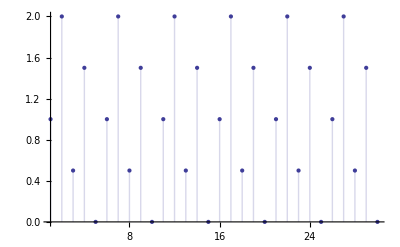

```mathematica
DiscretePlot[s2m[n,1,5/2],{n,1,30}]
```

```mathematica
DiscretePlot[Mod[n,5/2],{n,1,30}]
```

-Graphics-

```mathematica
Table[{n,aa=s2m[n,1,5/2],bb=Mod[n,5/2],aa-bb},{n,1,30,.3}]//TableForm
```

1. | 1 | 1. | 0.
1.3 | 1 | 1.3 | -0.3
1.6 | 1 | 1.6 | -0.6
1.9 | 1 | 1.9 | -0.9
2.2 | 2 | 2.2 | -0.2
2.5 | -1/2 | 0. | -0.5
2.8 | -1/2 | 0.3 | -0.8
3.1 | 1/2 | 0.6 | -0.1
3.4 | 1/2 | 0.9 | -0.4
3.7 | 1/2 | 1.2 | -0.7
4. | 3/2 | 1.5 | 0.
4.3 | 3/2 | 1.8 | -0.3
4.6 | 3/2 | 2.1 | -0.6
4.9 | 3/2 | 2.4 | -0.9
5.2 | 0 | 0.2 | -0.2
5.5 | 0 | 0.5 | -0.5
5.8 | 0 | 0.8 | -0.8
6.1 | 1 | 1.1 | -0.1
6.4 | 1 | 1.4 | -0.4
6.7 | 1 | 1.7 | -0.7
7. | 2 | 2. | 0.
7.3 | 2 | 2.3 | -0.3
7.6 | -1/2 | 0.1 | -0.6
7.9 | -1/2 | 0.4 | -0.9
8.2 | 1/2 | 0.7 | -0.2
8.5 | 1/2 | 1. | -0.5
8.8 | 1/2 | 1.3 | -0.8
9.1 | 3/2 | 1.6 | -0.1
9.4 | 3/2 | 1.9 | -0.4
9.7 | 3/2 | 2.2 | -0.7
10. | 0 | 0. | 0.
10.3 | 0 | 0.3 | -0.3
10.6 | 0 | 0.6 | -0.6
10.9 | 0 | 0.9 | -0.9
11.2 | 1 | 1.2 | -0.2
11.5 | 1 | 1.5 | -0.5
11.8 | 1 | 1.8 | -0.8
12.1 | 2 | 2.1 | -0.1
12.4 | 2 | 2.4 | -0.4
12.7 | -1/2 | 0.2 | -0.7
13. | 1/2 | 0.5 | 0.
13.3 | 1/2 | 0.8 | -0.3
13.6 | 1/2 | 1.1 | -0.6
13.9 | 1/2 | 1.4 | -0.9
14.2 | 3/2 | 1.7 | -0.2
14.5 | 3/2 | 2. | -0.5
14.8 | 3/2 | 2.3 | -0.8
15.1 | 0 | 0.1 | -0.1
15.4 | 0 | 0.4 | -0.4
15.7 | 0 | 0.7 | -0.7
16. | 1 | 1. | 0.
16.3 | 1 | 1.3 | -0.3
16.6 | 1 | 1.6 | -0.6
16.9 | 1 | 1.9 | -0.9
17.2 | 2 | 2.2 | -0.2
17.5 | -1/2 | 0. | -0.5
17.8 | -1/2 | 0.3 | -0.8
18.1 | 1/2 | 0.6 | -0.1
18.4 | 1/2 | 0.9 | -0.4
18.7 | 1/2 | 1.2 | -0.7
19. | 3/2 | 1.5 | 0.
19.3 | 3/2 | 1.8 | -0.3
19.6 | 3/2 | 2.1 | -0.6
19.9 | 3/2 | 2.4 | -0.9
20.2 | 0 | 0.2 | -0.2
20.5 | 0 | 0.5 | -0.5
20.8 | 0 | 0.8 | -0.8
21.1 | 1 | 1.1 | -0.1
21.4 | 1 | 1.4 | -0.4
21.7 | 1 | 1.7 | -0.7
22. | 2 | 2. | 0.
22.3 | 2 | 2.3 | -0.3
22.6 | -1/2 | 0.1 | -0.6
22.9 | -1/2 | 0.4 | -0.9
23.2 | 1/2 | 0.7 | -0.2
23.5 | 1/2 | 1. | -0.5
23.8 | 1/2 | 1.3 | -0.8
24.1 | 3/2 | 1.6 | -0.1
24.4 | 3/2 | 1.9 | -0.4
24.7 | 3/2 | 2.2 | -0.7
25. | 0 | 0. | 0.
25.3 | 0 | 0.3 | -0.3
25.6 | 0 | 0.6 | -0.6
25.9 | 0 | 0.9 | -0.9
26.2 | 1 | 1.2 | -0.2
26.5 | 1 | 1.5 | -0.5
26.8 | 1 | 1.8 | -0.8
27.1 | 2 | 2.1 | -0.1
27.4 | 2 | 2.4 | -0.4
27.7 | -1/2 | 0.2 | -0.7
28. | 1/2 | 0.5 | 0.
28.3 | 1/2 | 0.8 | -0.3
28.6 | 1/2 | 1.1 | -0.6
28.9 | 1/2 | 1.4 | -0.9
29.2 | 3/2 | 1.7 | -0.2
29.5 | 3/2 | 2. | -0.5
29.8 | 3/2 | 2.3 | -0.8

```mathematica
Table[{n, s2m[n,1,a=5/2],s2m[n-1,1,a],nmod[n,a],Mod[n,a],Mod[n-1,a]},{n,1,30,.3}]//TableForm
```

1. | 1 | 0 | 1 | 1. | 0.
1.3 | 1 | 0 | 1 | 1.3 | 0.3
1.6 | 1 | 0 | 1 | 1.6 | 0.6
1.9 | 1 | 0 | 1 | 1.9 | 0.9
2.2 | 2 | 1 | 1 | 2.2 | 1.2
2.5 | -1/2 | 1 | -3/2 | 0. | 1.5
2.8 | -1/2 | 1 | -3/2 | 0.3 | 1.8
3.1 | 1/2 | 2 | -3/2 | 0.6 | 2.1
3.4 | 1/2 | 2 | -3/2 | 0.9 | 2.4
3.7 | 1/2 | -1/2 | 1 | 1.2 | 0.2
4. | 3/2 | 1/2 | 1 | 1.5 | 0.5
4.3 | 3/2 | 1/2 | 1 | 1.8 | 0.8
4.6 | 3/2 | 1/2 | 1 | 2.1 | 1.1
4.9 | 3/2 | 1/2 | 1 | 2.4 | 1.4
5.2 | 0 | 3/2 | -3/2 | 0.2 | 1.7
5.5 | 0 | 3/2 | -3/2 | 0.5 | 2.
5.8 | 0 | 3/2 | -3/2 | 0.8 | 2.3
6.1 | 1 | 0 | 1 | 1.1 | 0.1
6.4 | 1 | 0 | 1 | 1.4 | 0.4
6.7 | 1 | 0 | 1 | 1.7 | 0.7
7. | 2 | 1 | 1 | 2. | 1.
7.3 | 2 | 1 | 1 | 2.3 | 1.3
7.6 | -1/2 | 1 | -3/2 | 0.1 | 1.6
7.9 | -1/2 | 1 | -3/2 | 0.4 | 1.9
8.2 | 1/2 | 2 | -3/2 | 0.7 | 2.2
8.5 | 1/2 | -1/2 | 1 | 1. | 0.
8.8 | 1/2 | -1/2 | 1 | 1.3 | 0.3
9.1 | 3/2 | 1/2 | 1 | 1.6 | 0.6
9.4 | 3/2 | 1/2 | 1 | 1.9 | 0.9
9.7 | 3/2 | 1/2 | 1 | 2.2 | 1.2
10. | 0 | 3/2 | -3/2 | 0. | 1.5
10.3 | 0 | 3/2 | -3/2 | 0.3 | 1.8
10.6 | 0 | 3/2 | -3/2 | 0.6 | 2.1
10.9 | 0 | 3/2 | -3/2 | 0.9 | 2.4
11.2 | 1 | 0 | 1 | 1.2 | 0.2
11.5 | 1 | 0 | 1 | 1.5 | 0.5
11.8 | 1 | 0 | 1 | 1.8 | 0.8
12.1 | 2 | 1 | 1 | 2.1 | 1.1
12.4 | 2 | 1 | 1 | 2.4 | 1.4
12.7 | -1/2 | 1 | -3/2 | 0.2 | 1.7
13. | 1/2 | 2 | -3/2 | 0.5 | 2.
13.3 | 1/2 | 2 | -3/2 | 0.8 | 2.3
13.6 | 1/2 | -1/2 | 1 | 1.1 | 0.1
13.9 | 1/2 | -1/2 | 1 | 1.4 | 0.4
14.2 | 3/2 | 1/2 | 1 | 1.7 | 0.7
14.5 | 3/2 | 1/2 | 1 | 2. | 1.
14.8 | 3/2 | 1/2 | 1 | 2.3 | 1.3
15.1 | 0 | 3/2 | -3/2 | 0.1 | 1.6
15.4 | 0 | 3/2 | -3/2 | 0.4 | 1.9
15.7 | 0 | 3/2 | -3/2 | 0.7 | 2.2
16. | 1 | 0 | 1 | 1. | 0.
16.3 | 1 | 0 | 1 | 1.3 | 0.3
16.6 | 1 | 0 | 1 | 1.6 | 0.6
16.9 | 1 | 0 | 1 | 1.9 | 0.9
17.2 | 2 | 1 | 1 | 2.2 | 1.2
17.5 | -1/2 | 1 | -3/2 | 0. | 1.5
17.8 | -1/2 | 1 | -3/2 | 0.3 | 1.8
18.1 | 1/2 | 2 | -3/2 | 0.6 | 2.1
18.4 | 1/2 | 2 | -3/2 | 0.9 | 2.4
18.7 | 1/2 | -1/2 | 1 | 1.2 | 0.2
19. | 3/2 | 1/2 | 1 | 1.5 | 0.5
19.3 | 3/2 | 1/2 | 1 | 1.8 | 0.8
19.6 | 3/2 | 1/2 | 1 | 2.1 | 1.1
19.9 | 3/2 | 1/2 | 1 | 2.4 | 1.4
20.2 | 0 | 3/2 | -3/2 | 0.2 | 1.7
20.5 | 0 | 3/2 | -3/2 | 0.5 | 2.
20.8 | 0 | 3/2 | -3/2 | 0.8 | 2.3
21.1 | 1 | 0 | 1 | 1.1 | 0.1
21.4 | 1 | 0 | 1 | 1.4 | 0.4
21.7 | 1 | 0 | 1 | 1.7 | 0.7
22. | 2 | 1 | 1 | 2. | 1.
22.3 | 2 | 1 | 1 | 2.3 | 1.3
22.6 | -1/2 | 1 | -3/2 | 0.1 | 1.6
22.9 | -1/2 | 1 | -3/2 | 0.4 | 1.9
23.2 | 1/2 | 2 | -3/2 | 0.7 | 2.2
23.5 | 1/2 | -1/2 | 1 | 1. | 0.
23.8 | 1/2 | -1/2 | 1 | 1.3 | 0.3
24.1 | 3/2 | 1/2 | 1 | 1.6 | 0.6
24.4 | 3/2 | 1/2 | 1 | 1.9 | 0.9
24.7 | 3/2 | 1/2 | 1 | 2.2 | 1.2
25. | 0 | 3/2 | -3/2 | 0. | 1.5
25.3 | 0 | 3/2 | -3/2 | 0.3 | 1.8
25.6 | 0 | 3/2 | -3/2 | 0.6 | 2.1
25.9 | 0 | 3/2 | -3/2 | 0.9 | 2.4
26.2 | 1 | 0 | 1 | 1.2 | 0.2
26.5 | 1 | 0 | 1 | 1.5 | 0.5
26.8 | 1 | 0 | 1 | 1.8 | 0.8
27.1 | 2 | 1 | 1 | 2.1 | 1.1
27.4 | 2 | 1 | 1 | 2.4 | 1.4
27.7 | -1/2 | 1 | -3/2 | 0.2 | 1.7
28. | 1/2 | 2 | -3/2 | 0.5 | 2.
28.3 | 1/2 | 2 | -3/2 | 0.8 | 2.3
28.6 | 1/2 | -1/2 | 1 | 1.1 | 0.1
28.9 | 1/2 | -1/2 | 1 | 1.4 | 0.4
29.2 | 3/2 | 1/2 | 1 | 1.7 | 0.7
29.5 | 3/2 | 1/2 | 1 | 2. | 1.
29.8 | 3/2 | 1/2 | 1 | 2.3 | 1.3

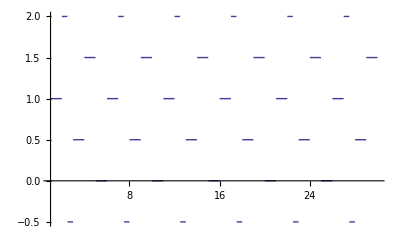

```mathematica
Plot[s2m[n,1,5/2],{n,1,30}]
```

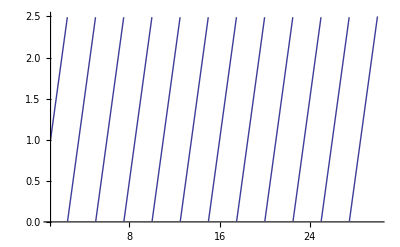

```mathematica
Plot[Mod[n,5/2],{n,1,30}]
```